```mathematica
E1[n_,k_,x_]:=Sum[E1[n/j,k-1,x],{j,1,n}]-x Sum[E1[n/(x j),k-1,x],{j,1,n/x}];E1[n_,0,x_]:=1
E2[n_,k_,x_]:=E2[n,k,x]=Sum[E2[n/j,k-1,x],{j,2,n}]-x Sum[E2[n/(x j),k-1,x],{j,1,n/x}];E2[n_,0,x_]:=1
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
E1Alt[n_,z_,x_]:=Sum[bin[z,k] E2[n,k,x],{k,0,Log[If[ x<2,x,2],n]}]
zeros[n_, x_] := zeros[n,x] = List@@NRoots[E1Alt[n,z,x]==0,z][[All,2]]
```

```mathematica
Expand[E1Alt[ 10, z,1.1]]
```

1-3.27641 z+5.48472 z^2-5.97008 z^3+4.86101 z^4-3.06271 z^5+1.48555 z^6-0.557369 z^7+0.169716 z^8-0.0413481 z^9+0.00803162 z^10-0.00124643 z^11+0.00015447 z^12-0.0000153414 z^13+1.22862×10^-6 z^14-7.97563×10^-8 z^15+4.20639×10^-9 z^16-1.80066×10^-10 z^17+6.22029×10^-12 z^18-1.7114×10^-13 z^19+3.66415×10^-15 z^20-5.88043×10^-17 z^21+6.65205×10^-19 z^22-4.72792×10^-21 z^23+1.58752×10^-23 z^24

```mathematica
zeros[ 10, 1.1]
```

{0.0444587-3.42988 ⅈ,0.0444587+3.42988 ⅈ,0.0546023-1.48706 ⅈ,0.0546023+1.48706 ⅈ,0.795269-0.646218 ⅈ,0.795269+0.646218 ⅈ,1.46544-0.713603 ⅈ,1.46544+0.713603 ⅈ,2.36265-6.22156 ⅈ,2.36265+6.22156 ⅈ,5.85488-14.1717 ⅈ,5.85488+14.1717 ⅈ,6.20902-23.4675 ⅈ,6.20902+23.4675 ⅈ,8.1197,12.8107-5.87752 ⅈ,12.8107+5.87752 ⅈ,23.7113-13.883 ⅈ,23.7113+13.883 ⅈ,28.9035-27.9333 ⅈ,28.9035+27.9333 ⅈ,29.1542,48.0603-12.3423 ⅈ,48.0603+12.3423 ⅈ}

```mathematica
zeros[ 100, 1.2]
```

{-5.86998-7.85834 ⅈ,-5.86998+7.85834 ⅈ,-1.9926-3.1597 ⅈ,-1.9926+3.1597 ⅈ,-1.96676-2.07497 ⅈ,-1.96676+2.07497 ⅈ,0.35708-1.03283 ⅈ,0.35708+1.03283 ⅈ,0.468404,0.752205,3.64989-0.978101 ⅈ,3.64989+0.978101 ⅈ,5.92397-5.95277 ⅈ,5.92397+5.95277 ⅈ,6.80322-16.2372 ⅈ,6.80322+16.2372 ⅈ,17.4628-1.98367 ⅈ,17.4628+1.98367 ⅈ,21.8002,26.2825-25.0348 ⅈ,26.2825+25.0348 ⅈ,41.406-29.4914 ⅈ,41.406+29.4914 ⅈ,56.8501-41.1016 ⅈ,56.8501+41.1016 ⅈ}

$Aborted

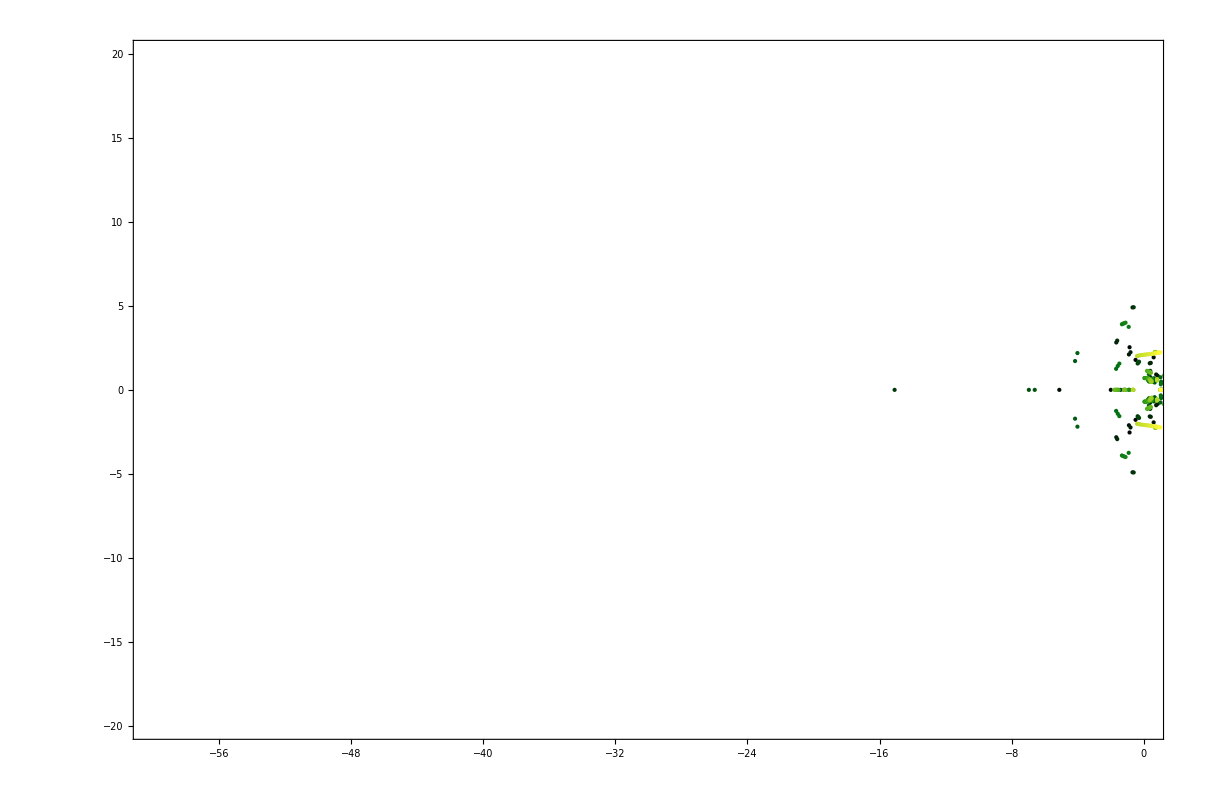

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 1.2;bb = 2-aa;
pts2=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros[100, n],{n,aa,aa+bb, .01}];
Graphics[pts2,Frame->True,PlotRange->{{-60,0},{-20,20}}]
```

```mathematica
E2a[n_,k_,x_]:=E2a[n+1,k-1,x]-x E2a[2n+1,k-1,x];E2a[n_,0,x_]:="wit"
```

```mathematica
Expand[E2a[109,4,x]]
```

wit-4 wit x+6 wit x^2-4 wit x^3+wit x^4

```mathematica
E2[1000,2,11/10]
```

83/5

```mathematica
aa = (11/10);nn = 1000;
Sum[ 1, {j,2,Floor[nn]},{k,2,Floor[nn/j]}] - 2 aa Sum[ 1, {j,1,Floor[nn/aa]}, {k,2,Floor[nn/( aa j )]}] + aa^2Sum[ 1, {j,1,Floor[nn/aa]},{k, 1, Floor[nn/(j aa^2 )]}]
Sum[ 1, {j,2,Floor[nn]},{k,2,Floor[nn/j]}] - 2 aa Sum[ 1, {j,2,nn}, {k,1,Floor[nn/( aa j )]}] + aa^2Sum[ 1, {j,1,Floor[nn/aa]},{k, 1, Floor[nn/(j aa^2 )]}]
```

83/5

83/5

```mathematica
E2[1000,3,1.73]
```

-526.961

```mathematica
aa = 1.73;nn = 1000;
Sum[ 1, {j,2,Floor[nn]},{k,2,Floor[nn/j]}, { l, 2, Floor[nn/(j k )]}] -
 3 aa Sum[ 1, {j,1,Floor[nn/aa]}, {k,2,Floor[nn/( aa j )]}, {l,2,Floor[nn/( aa j k)]}] +
 3 aa^2 Sum[ 1, {j,1,Floor[nn/aa]}, {k,1,Floor[nn/( aa^2 j )]}, {l, 2, Floor[nn/(aa^2 j k )]}] -
 aa^3Sum[ 1, {j,1,Floor[nn/aa]},{k, 1, Floor[nn/(j aa^2 )]}, {l, 1, Floor[nn/(j k aa^3)]}]
```

-526.961

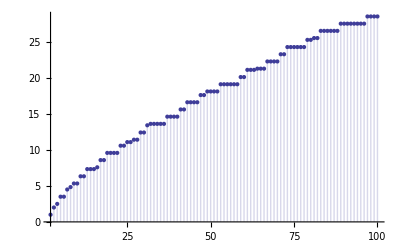

```mathematica
cc = 6/5;
DiscretePlot[Sum[cc^j/j,{j,1,Log[cc,n]}]+ D[ E1Alt[ n, z,cc],z]/.z->0,{n,2,100}]
```

```mathematica
E2b2[n_,0, x_] := 1
E2b2[n_, k_, x_] := E2b2[n,k,x]=Sum[ E2b2[ n/j,k-1,x],{j,2,Floor[n]}]
E2b1[n_, 0,0, x_] := 1
E2b1[n_, 0, k2_, x_] :=  E2b2[n,k2,x]
E2b1[n_, k1_, k2_, x_] := E2b1[n,k1,k2,x]=Sum[ E2b1[n/(j x), k1-1, k2, x],{j,1,Floor[n/x]}]
E2b[ n_, k_, x_] := Sum[ (-1)^(j) Binomial[ k,j] x^j E2b1[n,j,k-j,x],{j,0,k}]
E2bm[ n_, k_, x_] := Sum[ (-1)^(k-j) Binomial[ k,k-j] x^(k-j) E2b1[n,k-j,j,x],{j,0,Min[k,Floor[Log[2,n]]]}]
```

```mathematica
aa^3Sum[ 1, {j,1,Floor[nn/aa]},{k, 1, Floor[nn/(j aa^2 )]}, {l, 1, Floor[nn/(j k aa^3)]}]
```

18277.3

```mathematica
E2[120,64,103/99]
```

832524536290077543216399922016413481063815467129946006359415091052674576889803239695237129441446868023154173958830762763945721338859/17519882917518744496479284793694675989649338050187388530654455364919677998074409004683948399828593600887618898319662125318717867

```mathematica
E2b[4000,8,4/3]
```

1419657991/6561

```mathematica
E2bm[120,64,103/99]
```

832524536290077543216399922016413481063815467129946006359415091052674576889803239695237129441446868023154173958830762763945721338859/17519882917518744496479284793694675989649338050187388530654455364919677998074409004683948399828593600887618898319662125318717867

```mathematica
Floor[Log[2,100]]
```

6

```mathematica
E2c2[n_,0, x_] := 1
E2c2[n_, k_, x_] := E2c2[n,k,x]=Sum[ E2c2[ n/j,k-1,x],{j,2,Floor[n]}]
E2c1[n_, 0,0, x_] := 1
E2c1[n_, 0, k2_, x_] :=  E2c2[n,k2,x]
E2c1[n_, k1_, k2_, x_] := E2c1[n,k1,k2,x]=Sum[ E2c1[n/j, k1-1, k2, x],{j,1,Floor[n]}]
E2c[ n_, k_, x_] := Sum[ (-1)^j Binomial[ k,j] x^j E2c1[n/x^j,j,k-j,x],{j,0,k}]
E2cm[ n_, k_, x_] := Sum[ (-1)^(k-j) Binomial[ k,k-j] x^(k-j) E2c1[n/x^(k-j),k-j,j,x],{j,0,Min[k,Floor[Log[2,n]]]}]
E2cnull[ n_, k_, x_] := Sum[ (-1)^(k-j) Binomial[ k,k-j] x^(k-j) E2n[n/x^(k-j),k-j,j,x],{j,0,Min[k,Floor[Log[2,n]]]}]
E2cnullp[ n_, k_, x_] := (1 + (-1)^(k+1) Sum[ (-1)^(k-j) Binomial[ k,k-j] x^(k-j) E2n[n/x^(k-j),k-j,j,x],{j,0,Min[k,Floor[Log[2,n]]]}])/k
pp[ n_, x_] := Sum[x^j/j,{j,1,Log[x,n]}]+ Sum[ (-1)^(k+1)/k E2cm[ n,k,x],{k,1,Log[If[x<2,x,2],n]}]
pp2[ n_, x_] := Sum[ (-1)^(k+1)/k E2cm[ n,k,x],{k,1,Log[If[x<2,x,2],n]}]
pp2a[ n_, x_] := Sum[x^j/j,{j,1,Log[x,n]}]
pp2null[ n_, x_] := Table[ Expand[(-1)^(k+1)/k E2cnull[ n,k,x]],{k,1,Log[If[x<2,x,2],n]}]//TableForm
```

```mathematica
E2cm[120,64,103/99]
```

832524536290077543216399922016413481063815467129946006359415091052674576889803239695237129441446868023154173958830762763945721338859/17519882917518744496479284793694675989649338050187388530654455364919677998074409004683948399828593600887618898319662125318717867

```mathematica
E2c[120,64,103/99]
```

832524536290077543216399922016413481063815467129946006359415091052674576889803239695237129441446868023154173958830762763945721338859/17519882917518744496479284793694675989649338050187388530654455364919677998074409004683948399828593600887618898319662125318717867

```mathematica
pp2null[5,1.01]
```

```mathematica
E2cnullp[10000, 1,x]
```

1+E2n[10000,0,1,x]-x E2n[10000/x,1,0,x]

```mathematica
E2cnullp[10000, 2,x]
```

1/2 (1-E2n[10000,0,2,x]-x^2 E2n[10000/x^2,2,0,x]+2 x E2n[10000/x,1,1,x])

```mathematica
E2cnullp[10000, 3,x]
```

1/3 (1+E2n[10000,0,3,x]-x^3 E2n[10000/x^3,3,0,x]+3 x^2 E2n[10000/x^2,2,1,x]-3 x E2n[10000/x,1,2,x])

```mathematica
E2cnullp[10000, 4,x]
```

1/4 (1-E2n[10000,0,4,x]-x^4 E2n[10000/x^4,4,0,x]+4 x^3 E2n[10000/x^3,3,1,x]-6 x^2 E2n[10000/x^2,2,2,x]+4 x E2n[10000/x,1,3,x])